## Writing Algortihms :

### Bisection method with do (( for loop ))

x=0.5       f[s]=-0.377583

x=0.75       f[s]=0.0183111

x=0.625       f[s]=-0.185963

x=0.6875       f[s]=-0.0853349

x=0.71875       f[s]=-0.0338794

x=0.734375       f[s]=-0.00787473

x=0.742188       f[s]=0.00519571

x=0.738281       f[s]=-0.00134515

x=0.740234       f[s]=0.00192387

x=0.739258       f[s]=0.000289009

x=0.73877       f[s]=-0.000528158

x=0.739014       f[s]=-0.000119597

x=0.739136       f[s]=0.0000847007

x=0.739075       f[s]=-0.0000174493

x=0.739105       f[s]=0.0000336253

x=0.73909       f[s]=8.08791×10^-6

x=0.739082       f[s]=-4.68074×10^-6

x=0.739086       f[s]=1.70358×10^-6

x=0.739084       f[s]=-1.48858×10^-6

x=0.739085       f[s]=1.07502×10^-7

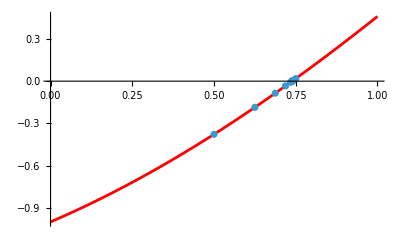

```mathematica
f[x_] = x - Cos[x];
p = Plot[f[x], {x, 0, 1}, PlotStyle->Red];
a = 0; b = 1;
lis = {};
Do[
s = N[(a + b)/2];
If[f[s]*f[a] < 0, b=s, a = s];
lis = Append[lis, {s, f[s]}];
Print["x=", s, "       ", "f[s]=", f[s]], 
{i, 1, 20}
]
q = ListPlot[lis];
Show[p, q]
```

### Bisection Method using While

x=1.5       f[s]=0.252505

x=1.25       f[s]=-0.386485

x=1.375       f[s]=-0.0902681

x=1.4375       f[s]=0.0752771

x=1.40625       f[s]=-0.00895371

x=1.42188       f[s]=0.0327968

x=1.41406       f[s]=0.0118304

x=1.41016       f[s]=0.00141554

x=1.4082       f[s]=-0.00377478

x=1.40918       f[s]=-0.00118104

x=1.40967       f[s]=0.000116895

x=1.40942       f[s]=-0.000532162

x=1.40955       f[s]=-0.000207656

x=1.40961       f[s]=-0.0000453859

x=1.40964       f[s]=0.0000357532

x=1.40962       f[s]=-4.81668×10^-6

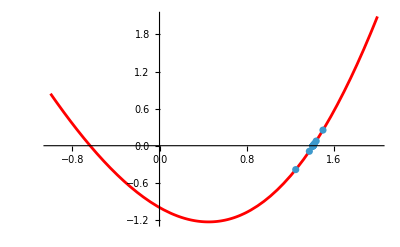

```mathematica
g[x_] = Power[x,2] - Sin[x]-1;
p = Plot[g[x], {x, -1, 2}, PlotStyle->Red];
a = 1; b = 2;
lis = {};
s = (a+b)/2;
While[Abs[g[s]] > .00001,
s = N[(a + b)/2];
If[g[s]*g[a] < 0, b=s, a = s];
lis = Append[lis, {s, g[s]}];
Print["x=", s, "       ", "f[s]=", g[s]]
]
q = ListPlot[lis];
Show[p, q]
```